```mathematica
(*big_G_force_Fourier_amplitude.nb: Mathematic notebook version; takes only first oscillation corresponding to mean geometry
G_2_cylinder_20240228.mm:calculates force with augmented test masses and counterweight.
G_1_cylinder_20240225.mm:calculates force with augmented test masses:needs only silicon density.
fourier_newtonian_point_point_err_20240209.mm:run in NH folder.
fourier_newtonian_point_point_err_20230810.mm:include error bars.
fourier_newtonian_point_point_20230802.mm:convert Newtonian unscaled virtual work to force;compare point-point approx.
fourier_newtonian_20230720.mm:convert Newtonian unscaled virtual work to force 
fourier_vpp_std_20230308.mm:convert Vpp unscaled virtual work to Force 
fourier_vpp_point_point_AD_20230215.mm:scale MC by (microns/meters)^2 and (1/c),clear all variables,semicolons,print more results.
fourier_vpp_point_point_AD_20230214.mm:runs in 20230214 folder.
fourier_vpp_point_point_AD_20230126.mm:version from AD.
fourier_vpp_point_point_202221111.mm:plot vpp,compare point-point approx.
fourier_ariadne_torque_20200531.mm:plot ariadne torque and calculate amplitudes.
fourier_force_probe_20200422.mm:calculate fourier amplitude of force at probe,clean up code.
fourier_stats_v1_20200422_2.mm:replace obsolete ErrorBarPlots with About function 
fourier_stats_v1_20200422.mm:first working version on Carbonate (path specification in OpenRead cmd) fourier_stats.mm:reads virtual work and phase data from MC,plots,computes Fourier amplitudes different ways*)
```

```mathematica
Clear[G,ps,mtm,amp,k,fstring,VRawDatf,VRawDat];
(*force parameters*)
G=6.67 10^-11;           (*Newton constant,Nm^2/kg^2*)
ps=2.329 10^3;           (*silicon density,kg/m^3*)
mtm=1.0 10^-6;          (*microns to m*)
amp=0.273;                      (*amplitude of COMSOL large rectangle rear corner[probe location],um*)
(*amp=1.0;*)                          (*amplitude of detector in simple translational mode,um*)
k=mtm^4 G ps ps/amp; (*MC to force conversion factor*)

(*Enter virtual work data file as string*)
fstring="big_G_W_phase.txt";

(*Open data files for reading*)
VRawDatf=Import["C:\\Users\\jcl\\OneDrive - University of Illinois - Urbana\\long_group\\experiment\\Torsion_Oscillator\\big_G\\sensitivity\\planck\\"<>fstring,"Table"];
VRawDat=Take[VRawDatf,{2,9}];
```

```mathematica
Clear[dimf,pRawDat,mRawDat,eRawDat,pmin,pmax,bxmin,bxmax,xRaw,xRawPlt,prad,mRawDatm,ampmm,sampmc,campmc,ampmc,esampmc,ecampmc,eampmc];
(*Get number of phase points*)
dimf=Dimensions[VRawDat][[1]];

(*Separate X and Y data*)
pRawDat=VRawDat[[All,1]];
mRawDat=k VRawDat[[All,2]];
eRawDat=Abs[k VRawDat[[All,3]]];

(*Plot*)
pmin=Min[pRawDat];
pmax=Max[pRawDat];
bxmin=Min[mRawDat]-Max[eRawDat];
bxmax=Max[mRawDat]+Max[eRawDat];
xRaw=Table[{pRawDat[[i]],Around[mRawDat[[i]],eRawDat[[i]]]},{i,1,dimf}];
xRawPlt=ListPlot[xRaw,PlotStyle->{PointSize[.020]},PlotRange->{{pmin,pmax},{bxmin,bxmax}},PlotLabel->"Force vs. phase",GridLines->Automatic,AxesLabel->{"phi (rad)","F (N)"},Frame->True];
```

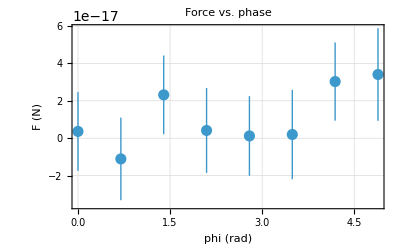

Static force            = 3.6189×10^-18 +/- 2.10028×10^-17 N

Fourier amplitude (MM)  = 1.00312×10^-17 N

Fourier amplitude (MC)  = 1.20547×10^-17 +/- 1.57199×10^-17 N

```mathematica
(*Fourier amplitudes*)
prad=pRawDat;

mRawDatm=mRawDat-Mean[mRawDat];

ampmm=Abs[2. Fourier[mRawDatm,FourierParameters->{-1,1}]]; (*Fourier amplitude from mm*)
sampmc=(2./dimf) Sum[mRawDatm[[j]] Sin[prad[[j]]],{j,1,dimf}]; (*Fourier amplitude as calculated in MC*)
campmc=(2./dimf) Sum[mRawDatm[[j]] Cos[prad[[j]]],{j,1,dimf}]; (*Fourier amplitude as calculated in MC*)
ampmc=Sqrt[sampmc^2+campmc^2];                               (*Total FA magnitude*)

(*FA errors*)
esampmc=(2./dimf) Sqrt[Sum[(eRawDat[[j]] Sin[prad[[j]]])^2,{j,1,dimf}]]; (*Fourier sine amplitude err as calculated in MC*)
ecampmc=(2./dimf) Sqrt[Sum[(eRawDat[[j]] Cos[prad[[j]]])^2,{j,1,dimf}]]; (*Fourier cosine amplitude err as calculated in MC*)
eampmc=Sqrt[esampmc^2+ecampmc^2];                               (*Total FA magnitude err*)

(*Show*)
Show[xRawPlt]
Print["Static force            ="," ",mRawDat[[1]]," +/- ",eRawDat[[1]]," N"]
Print["Fourier amplitude (MM)  ="," ",ampmm[[2]]," N"]
Print["Fourier amplitude (MC)  ="," ",ampmc," +/- ",eampmc," N"]
Print[" "]
```